# Night 6

### Clearing Variables

```mathematica
Clear["Global`*"]
```

### Defining Variables

```mathematica
f = -2*Cos[x*.8]+2;
density =300;
ballastmass = 5000;
xmin1 = -2;
xmax1 = 2;
ymin1 = 0;
ymax1 = 2;
zmin1 = 0;
zmax1 =10;
xballast = 0;
yballast = 0;
θ = 95;
```

### Calculating Mass and Center of Mass

```mathematica
MassFunc[f_,xmin1_,xmax1_,ymin1_,ymax1_,zmin1_,zmax1_,boatmass_,ballastmass_,xballast_,yballast_,density_]:=Module[{},
boat = ImplicitRegion[f<y<ymax1&&xmin1<x<xmax1&&ymin1<y<ymax1, {x,y}];

boatmass = zmax1*Integrate[density,{x, y}∈boat];

totalmass = boatmass+ballastmass;

xcomboat = ( 1/boatmass)*zmax1*Integrate[x*density,{x, y}∈boat];

ycomboat=N[( 1/boatmass)*zmax1*Integrate[y*density,{x, y}∈boat]];

xcom = 1/(totalmass)*(xcomboat*boatmass+xballast*ballastmass);

ycom = 1/(totalmass)*(ycomboat*boatmass+yballast*ballastmass);

com = {xcom,ycom,0};

{boat,com, totalmass}
]
```

```mathematica
MassFunc[f,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,boatmass,ballastmass,xballast,yballast,density]
```

{ImplicitRegion[2-2 Cos[0.8 x]<y<2&&-2<x<2&&0<y<2,{x,y}],{0.,0.910951,0},20000.}

### Function/Module

```mathematica
Salmon[f_,density_,ballastmass_,xmin1_,xmax1_,ymin1_,ymax1_,zmin1_,zmax1_,xballast_,yballast_,θ_, boat_, com_] := Module[{}, 
water = ImplicitRegion[If[θ<90, y<Tan[θ Degree]*x+d, y>Tan[θ Degree]*x+d],{{x,-2,2},{y,-2,2}}];

submerged = RegionIntersection[boat, water];

displacement = 1000*zmax1*RegionMeasure[submerged];

draft = N[d/.FindRoot[displacement==totalmass, {d, -20, 20}][[1]]];

cob = Append[RegionCentroid[submerged/.{d->draft}],0];

buoyancy = totalmass*98/10*{-Sin[ θ Degree],Cos[θ Degree],0};

torque = Cross[cob-com,buoyancy][[3]];

torque
]
```

### Testing Function

```mathematica
Salmon[f,density,ballastmass,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,xballast,yballast,θ, boat, com]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-2<x<2&&0<y<2&&2 Cos[0.8 x]+y>2&&d<Cot[5 °] x+y,{x,y}].

59991.6

### Plotting Results

```mathematica
ListPlot[Table[{θ,Salmon[f,density,ballastmass,xmin1,xmax1,ymin1,ymax1,zmin1,zmax1,xballast,yballast,θ, boat, com]},{θ,{0,10,20,30,40,50,60,70,80,100,110,120,130,140,150,160,170,180}}]]
```

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-2<x<2&&0<y<2&&d>y&&2 Cos[0.8 x]+y>2,{x,y}].

RegionMeasure::nmet: Unable to compute the measure of region ImplicitRegion[-2<x<2&&0<y<2&&-20.>y&&2 Cos[0.8 x]+y>2,{x,y}].

General::stop: Further output of RegionMeasure::nmet will be suppressed during this calculation.

FindRoot::nlnum: The function value {-20000.+10000. RegionMeasure[ImplicitRegion[-2.<x<2.&&0.<y<2.&&-20.>y&&Plus[«2»]>2.,{x,y}]]} is not a list of numbers with dimensions {1} at {d} = {-20.}.

ReplaceAll::reps: {10000 RegionMeasure[ImplicitRegion[-2<x<2&&0<y<2&&d>y&&Plus[«2»]>2,{x,y}]]==20000.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {10000. RegionMeasure[ImplicitRegion[-2.<x<2.&&0.<y<2.&&d>y&&Plus[«2»]>2.,{x,y}]]==20000.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ImplicitRegion::msgs: Evaluation of {-2<x<2&&0<y<2&&(d/.10000. RegionMeasure[ImplicitRegion[«2»]]==20000.)>y&&2 Cos[0.8 x]+y>2,True} generated message(s) {RegionMeasure::nmet,ReplaceAll::reps}.

RegionCentroid::nmet: Unable to compute the centroid of region ImplicitRegion[-2<x<2&&0<y<2&&(d/.10000. RegionMeasure[ImplicitRegion[«2»]]==20000.)>y&&2 Cos[0.8 x]+y>2,{x,y}].

RegionCentroid::nonopt: Options expected (instead of 0) beyond position 1 in RegionCentroid[ImplicitRegion[-2<x<2&&0<y<2&&(d/.10000. RegionMeasure[«1»]==20000.)>y&&2 Cos[Times[«2»]]+y>2,{x,y}],0]. An option must be a rule or a list of rules.

FindRoot::nlnum: The function value {-20000.+10000. RegionMeasure[ImplicitRegion[-2.<x<2.&&0.<y<2.&&Plus[«2»]>y&&Plus[«2»]>2.,{x,y}]]} is not a list of numbers with dimensions {1} at {d} = {-20.}.

ReplaceAll::reps: {10000 RegionMeasure[ImplicitRegion[-2<x<2&&0<y<2&&Plus[«2»]>y&&Plus[«2»]>2,{x,y}]]==20000.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ImplicitRegion::msgs: Evaluation of {-2<x<2&&0<y<2&&(d/.10000. RegionMeasure[«1»]==20000.)+x Tan[10 °]>y&&2 Cos[0.8 x]+y>2,True} generated message(s) {RegionMeasure::nmet,ReplaceAll::reps}.

RegionCentroid::nmet: Unable to compute the centroid of region ImplicitRegion[-2<x<2&&0<y<2&&(d/.10000. RegionMeasure[«1»]==20000.)+x Tan[10 °]>y&&2 Cos[0.8 x]+y>2,{x,y}].

RegionCentroid::nonopt: Options expected (instead of 0) beyond position 1 in RegionCentroid[ImplicitRegion[-2<x<2&&0<y<2&&(d/.Times[«2»]==20000.)+x Tan[Times[«2»]]>y&&2 Cos[Times[«2»]]+y>2,{x,y}],0]. An option must be a rule or a list of rules.

FindRoot::nlnum: The function value {-20000.+10000. RegionMeasure[ImplicitRegion[-2.<x<2.&&0.<y<2.&&Plus[«2»]>y&&Plus[«2»]>2.,{x,y}]]} is not a list of numbers with dimensions {1} at {d} = {-20.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ImplicitRegion::msgs: Evaluation of {-2<x<2&&0<y<2&&(d/.10000. RegionMeasure[«1»]==20000.)+x Tan[20 °]>y&&2 Cos[0.8 x]+y>2,True} generated message(s) {RegionMeasure::nmet,ReplaceAll::reps}.

General::stop: Further output of ImplicitRegion::msgs will be suppressed during this calculation.

RegionCentroid::nmet: Unable to compute the centroid of region ImplicitRegion[-2<x<2&&0<y<2&&(d/.10000. RegionMeasure[«1»]==20000.)+x Tan[20 °]>y&&2 Cos[0.8 x]+y>2,{x,y}].

General::stop: Further output of RegionCentroid::nmet will be suppressed during this calculation.

RegionCentroid::nonopt: Options expected (instead of 0) beyond position 1 in RegionCentroid[ImplicitRegion[-2<x<2&&0<y<2&&(d/.Times[«2»]==20000.)+x Tan[Times[«2»]]>y&&2 Cos[Times[«2»]]+y>2,{x,y}],0]. An option must be a rule or a list of rules.

General::stop: Further output of RegionCentroid::nonopt will be suppressed during this calculation.

### Visualizing Boat Shape

```mathematica
RegionPlot3D[f<y<ymax1&&xmin1<x<xmax1&&ymin1<y<ymax1, {x, -5, 5},{y, 0, 10},{z, zmin1, zmax1}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

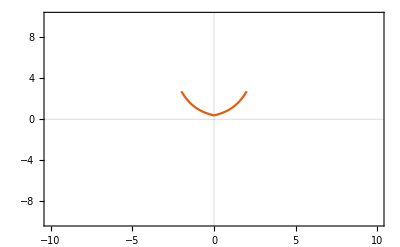

```mathematica
Show[Plot[(1)*Abs[Exp[x-1]], {x,0,2},PlotRange->{{-10,10},{-10,10}}, PlotTheme->"Scientific"],Plot[(1)*Abs[Exp[-x-1]], {x,-2,0},PlotRange->{{-10,10},{-10,10}}, PlotTheme->"Scientific"]]
```

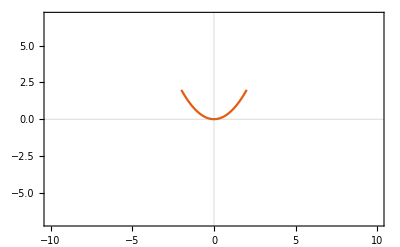

```mathematica
Plot[(1/2)*x^2, {x,-2,2},PlotRange->{{-10,10},{-7,7}}, PlotTheme->"Scientific"]
```

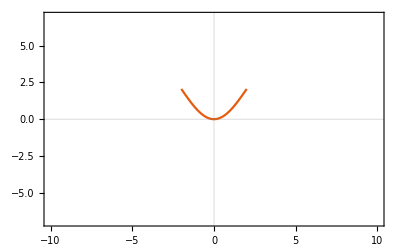

```mathematica
Plot[-2*Cos[x*.8]+2, {x,-2,2},PlotRange->{{-10,10},{-7,7}}, PlotTheme->"Scientific"]
```